```mathematica
p1=Plot[{13n+2,2 n^2+n},{n,0,8}, PlotStyle->{Blue,Orange}];
p2=Plot[{13n+2,2 n^2+n},{n,0,12},PlotStyle->{Blue,Orange}];
p3=Plot[{13n+2,2 n^2+n},{n,0,100},PlotStyle->{Blue,Orange}];
p4=Plot[{13n+2,2 n^2+n},{n,0,1000},PlotStyle->{Blue,Orange}];
```

```mathematica
Rasterize[Show[Legended[GraphicsGrid[{{p1,p2,p3,p4}}],LineLegend[{Blue,Orange},{13n+2,2 n^2+2}]],ImageSize->1700]]
```

-Graphics-

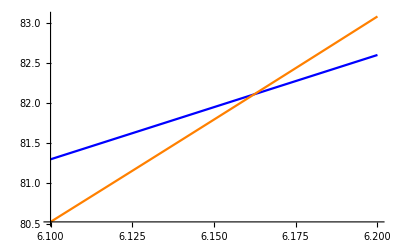

```mathematica
Plot[{13n+2,2 n^2+n},{n,6.1,6.2}, PlotStyle->{Blue, Orange}]
```

```mathematica
p1=Plot[{11n+1,(2n+4)},{n,0,1},PlotStyle->{Blue,Orange}];
p2=Plot[{11n+1,(2n+4)},{n,0,2},PlotStyle->{Blue,Orange}];
p3=Plot[{11n+1,(2n+4)},{n,0,10},PlotStyle->{Blue,Orange}];
p4=Plot[{11n+1,(2n+4)},{n,0,100},PlotStyle->{Blue,Orange}];
Rasterize[Show[Legended[GraphicsGrid[{{p1,p2,p3,p4}}],LineLegend[{Blue,Orange},{11n+1,(2n+4)}]],ImageSize->1700]]
```

-Graphics-

```mathematica
p1=Plot[{11n+1,10(2n+4)},{n,0,1},PlotStyle->{Blue,Orange}];
p2=Plot[{11n+1,10(2n+4)},{n,0,2},PlotStyle->{Blue,Orange}];
p3=Plot[{11n+1,10(2n+4)},{n,0,10},PlotStyle->{Blue,Orange}];
p4=Plot[{11n+1,10(2n+4)},{n,0,1000},PlotStyle->{Blue,Orange}];
Rasterize[Show[Legended[GraphicsGrid[{{p1,p2,p3,p4}}],LineLegend[{Blue,Orange},{11n+1,10(2n+4)}]],ImageSize->1700]]
```

-Graphics-

```mathematica
F[n_]:=4 n^2+30;
G[n_]:=2 n^3+n;
Legended[Manipulate[Show[Plot[{F[n],c G[n]},{n,0,maxN},PlotStyle->{Blue,Orange}],ImageSize-> Large, SaveDefinitions->True],{maxN,1,100},{{c,1},0,10}],LineLegend[{Blue,Orange},{F[n],c G[n]}]]
```

```mathematica
A[n_]:=2 n^3+10;
B[n_]:=4 n^2+30;

p1=Plot[{A[n],B[n]},{n,0,5},PlotStyle->{Blue,Orange}];
p2=Plot[{A[n],B[n]},{n,0,10},PlotStyle->{Blue,Orange}];
p3=Plot[{A[n],B[n]},{n,0,100},PlotStyle->{Blue,Orange}];
p4=Plot[{A[n],B[n]},{n,0,1000},PlotStyle->{Blue,Orange}];
Rasterize[Show[Legended[GraphicsGrid[{{p1,p2,p3,p4}}],LineLegend[{Blue,Orange},{A[n],B[n]}]],ImageSize->1700]]
```

-Graphics-

```mathematica
F[n_]:=4 n^2+30;
G[n_]:=2 n^2+n;
Legended[Manipulate[Show[Plot[{F[n],Subscript[c, 1] G[n],Subscript[c, 2] G[n]},{n,0,i},PlotStyle->{Blue,Orange,Green}],ImageSize-> Large, SaveDefinitions->True],{i,1,100},{{Subscript[c, 1],1},0,3},{{Subscript[c, 2],1},0,3}],LineLegend[{Blue,Orange,Green},{F[n],Subscript[c, 1] G[n],Subscript[c, 2] G[n]}]]
```

```mathematica
F[n_]:=4 n^2+30;
G[n_]:=2 n^2+n;
Subscript[c, 1] =1;
Subscript[c, 2]=3;

p1=Plot[{F[n],Subscript[c, 1] G[n],Subscript[c, 2] G[n]},{n,0,5},PlotStyle->{Blue,Orange, Green}];
p2=Plot[{F[n],Subscript[c, 1] G[n],Subscript[c, 2] G[n]},{n,0,10},PlotStyle->{Blue,Orange,Green}];
p3=Plot[{F[n],Subscript[c, 1] G[n],Subscript[c, 2] G[n]},{n,0,100},PlotStyle->{Blue,Orange,Green}];
p4=Plot[{F[n],Subscript[c, 1] G[n],Subscript[c, 2] G[n]},{n,0,1000},PlotStyle->{Blue,Orange,Green}];
Rasterize[Show[Legended[GraphicsGrid[{{p1,p2,p3,p4}}],LineLegend[{Blue,Orange,Green},{F[n],Subscript[c, 1] G[n],Subscript[c, 2] G[n]}]],ImageSize->1700]]
```

-Graphics-